```mathematica
Remove["Global`*"]
```

Remove::rmnsm: There are no symbols matching "Global`*".

### Definitions of the γ-compounding algebra

```mathematica
γ=1/2;
Expγ[x_] := If[γ==0, Exp[x], (1+γ x)^(1/γ)];
Logγ[x_] := If[γ==0, Log[x], (x^γ-1)/γ];
Clear[CircleTimes];
CircleTimes[x_,y_] := FullSimplify[PowerExpand[Expγ[Logγ[x] + Logγ[y]]]];
```

### Define parameters for simulations

```mathematica
X0 = 1;
T =50;
M = 50;
g = 21/20;
r = 9/20;
```

### Define analytical formulae

```mathematica
x[t_, g_] := X0 ⊗ Expγ[Logγ[g] t];
x2[t_, g_, r_] := X0⊗(1/2^t Sum[Binomial[t,n]Expγ[n Logγ[g+r]] ⊗ Expγ[(t-n)Logγ[g-r]], {n,0, t}]);
z[t_, g_, r_] := X0 ⊗ Expγ[Logγ[g] t];
f[x_, b_, g_, r_] := If[b ==0, x ⊗ (g+r), x ⊗ (g-r)]
```

### Generate some trajectories

```mathematica
X = Table[0,{i,1,T+1}, {j,1,M}];
B = Table[RandomInteger[{0,1}],{i,1,T}, {j,1,M}];
For[j=1, j<= M, j++, 
X[[1,j]]= X0;
For[i=2, i<= T+1, i++,
c = B[[i-1,j]];
X[[i,j]]= N[f[X[[i-1, j]], c, g, r]];
];

];
```

### Make some plots

Generate lin-lin plot for additive case, lin-log for the multiplicative case and log-log for the fractional case

```mathematica
SetOptions[{Plot,ListLogPlot, ListPlot, ListLogLogPlot},
Frame-> True,
LabelStyle->{FontFamily->"Arial", FontSize->12},
AspectRatio->1];
SetOptions[ListLogPlot,  Joined->True, FrameLabel->{"T (number of rounds)", "X_T (wealth)"}];
```

```mathematica
sampleTrajectories=TemporalData[X[[1;;T+1, 1;;M]],{Table[i-1, {i,1, T+1}]}];
F = Table[N[x2[t,g,r]],{t,0,T}];
expectedValue = TemporalData[F, {Table[i-1, {i,1, T+1}]}];

linestyles = Table[{GrayLevel[RandomReal[]], Thickness[0.002]}, {i,1,M}];
Switch[γ,
0
,
p1 = ListLogPlot[sampleTrajectories,PlotStyle->linestyles,PlotRange->All, Joined->True,  PlotLegends->Placed[{"Sample trajectories"}, {0.25, 0.95}]];
p2 = ListLogPlot[expectedValue,PlotStyle->{Blue,PointSize[.02]},PlotRange->All, Joined->True, PlotLegends->Placed[{"Expectation"}, {0.20, 0.85}]];
,
1
,
p1 = ListPlot[sampleTrajectories,PlotStyle->linestyles,PlotRange->All, Joined->True,  PlotLegends->Placed[{"Sample trajectories"}, {0.25, 0.95}]];
p2 = ListPlot[expectedValue,PlotStyle->{Blue,PointSize[.02]},PlotRange->All, Joined->True, PlotLegends->Placed[{"Expectation"}, {0.20, 0.85}]];
,
_
,
p1 = ListLogLogPlot[sampleTrajectories,PlotStyle->linestyles,PlotRange->All, Joined->True,  PlotLegends->Placed[{"Sample trajectories"}, {0.25, 0.95}]];
p2 = ListLogLogPlot[expectedValue,PlotStyle->{Blue,PointSize[.02]},PlotRange->All, Joined->True, PlotLegends->Placed[{"Expectation"}, {0.20, 0.85}]];
];
```

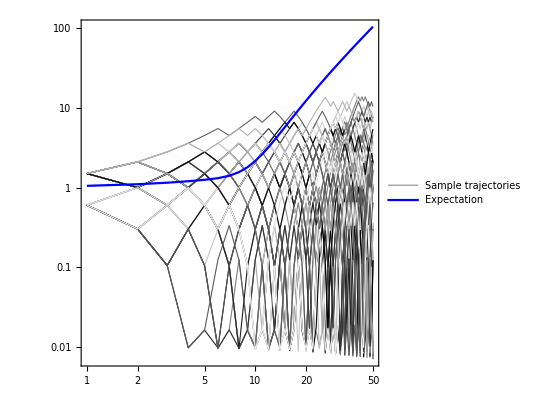

```mathematica
Show[p1,p2, PlotRange->All]
```

```mathematica
p1 = Plot[x2[t,g,r], {t, 0, 100}, PlotStyle->Blue];
p2 =  Plot[x[t,g], {t, 0, 100}, PlotStyle->Green];
```

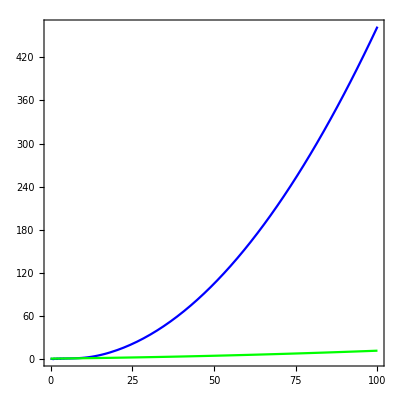

```mathematica
Show[p1,p2]
```

```mathematica
Table[Coefficient[x2[i,μ,σ], √(μ-σ) √(μ+σ)], {i,1,10}]
```

{0,1,3,6,10,15,21,28,36,45}

```mathematica
F = Table[x2[t,g,r],{t,0,10}]
```

{1,21/20,83/20-2 √(3/5)-√6+3/(√10),103/10-6 √(3/5)-3 √6+9/(√10),39/2+9 √(2/5)-12 √(3/5)-6 √6,127/4-10 √6+3 √10-4 √15,1/80 (3644-1140 √6+315 √10-450 √15),1/320 (18898-5705 √6+1260 √10-2184 √15),1/80 (5694-1615 √6+210 √10-588 √15),-36 √(3/5)+1/256 (20938-5445 √6),1/256 (23410-5465 √6-945 √10-1674 √15)}